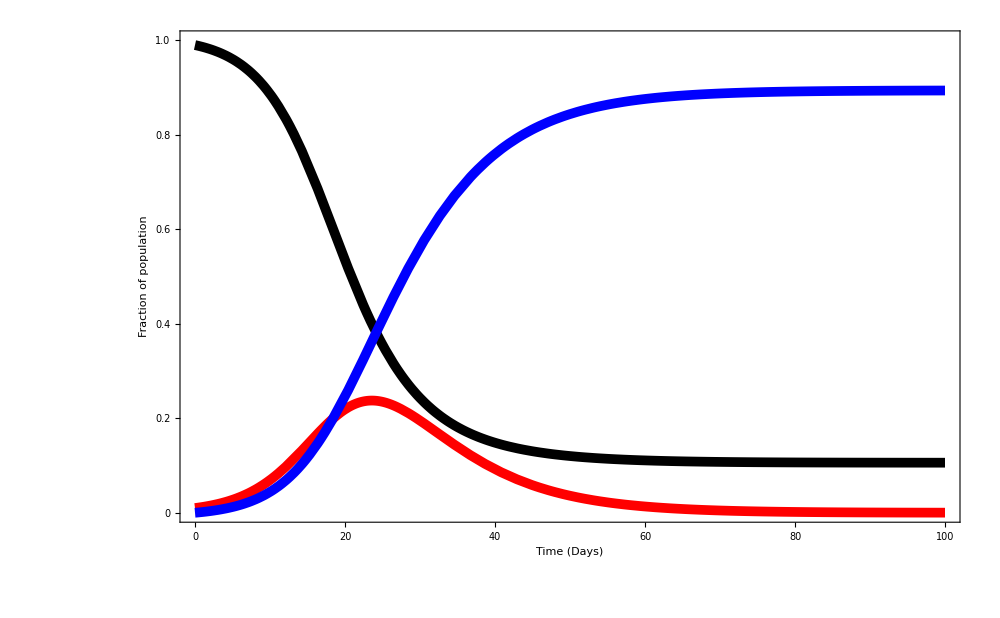

```mathematica
B=0.35; G=0.14;
Sol1=NDSolve[{S1'[t]==-B*S1[t]*I1[t],
I1'[t]== B*S1[t]*I1[t]-G*I1[t],
R1'[t]== G*I1[t],
S1[0]==0.99,I1[0]==0.01,R1[0]==0},{S1,I1,R1},{t,0,100}];
PS0=Plot[{S1[t]/.Sol1},{t,0,100},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of population",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Susceptible(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000];
PI0=Plot[{I1[t]/.Sol1},{t,0,100},PlotRange->{0,1},
PlotStyle->{Red,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]]},{Style["Infectious(RK-4)",Bold,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000];
PR0=Plot[{R1[t]/.Sol1},{t,0,100},PlotRange->{0,1},
PlotStyle->{Blue,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]]},{Style["Recovered(RK-4)",Bold,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000];
Show[PS0,PI0,PR0]
```

```mathematica
S0=S1[0]/.Sol1;
I0=I1[0]/.Sol1;
R0=R1[0]/.Sol1;
C1[0]=1;
C1[k_]:=Sum[Binomial[k-1,i-1]C1[k-i]b[i],{i,k}];
b[1]=B*I0;
b[n_]:=G*b[n-1]-B*S0*Sum[Binomial[n-2,i-1]C1[n-1-i]b[i],{i,n-1}];
SolSty=Solve[1-x+(G/B)*Log[x/S0 ]==0&&x≤1,x];
Sfty=x/.SolSty;
a0=Log[Sfty/S0];
b[0]=-a0;
Lam1=G-B*Sfty;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Sfty
```

{0.105894}

```mathematica
M15=Table[j^(i-1),{i,15},{j,15}];
b[0]=-a0;
N15=Table[b[i-1]/Lam1^(i-1),{i,15}];
Sol15=Inverse[M15].N15;
S15[x_]:=a0+Sum[Sol15[[i,1]]*Exp[-i*Lam1*x],{i,15}]
```

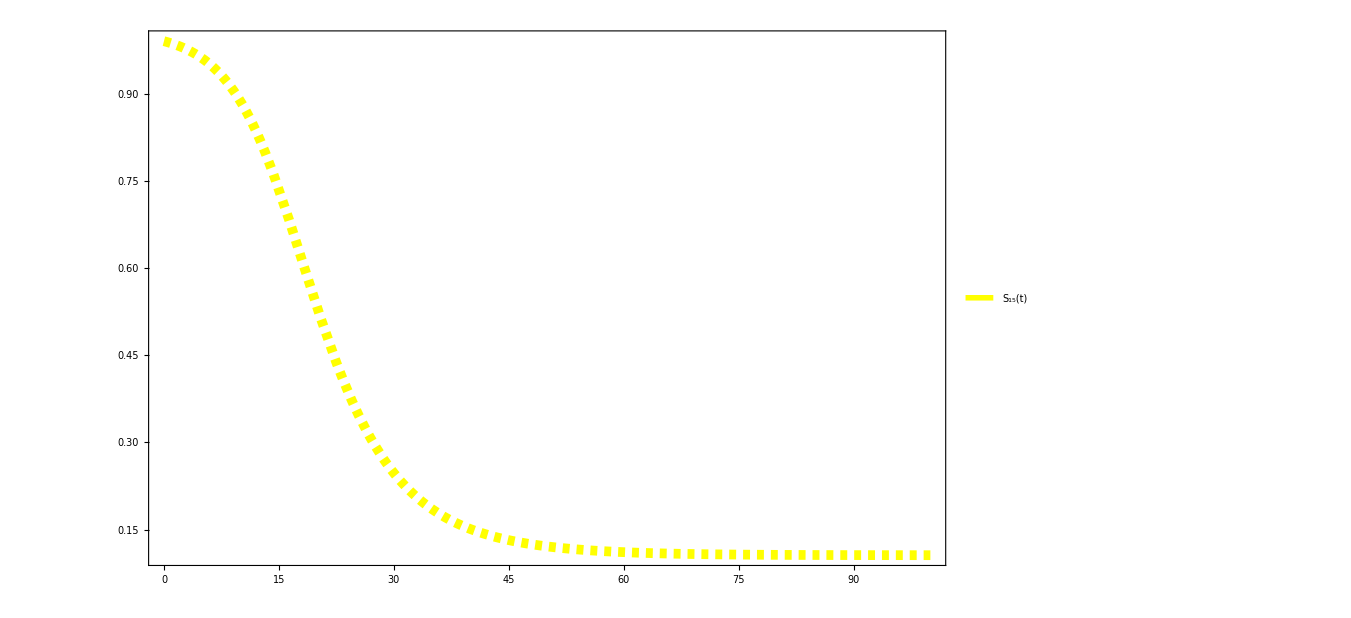

```mathematica
P15=Plot[S0*Exp[S15[x]],{x,0,100},
PlotStyle->{Yellow,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Yellow,Dashed,AbsoluteThickness[5]]},{Style["S_15(t)",Bold,Italic,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

```mathematica
S15[t]
```

{-2.23526+0.667927 ⅇ^(-1.54406 t)-10.1641 ⅇ^(-1.44112 t)+72.3135 ⅇ^(-1.33818 t)-319.195 ⅇ^(-1.23524 t)+978.052 ⅇ^(-1.13231 t)-2205.03 ⅇ^(-1.02937 t)+3781.85 ⅇ^(-0.926433 t)-5030.29 ⅇ^(-0.823496 t)+5240.03 ⅇ^(-0.720559 t)-4284.69 ⅇ^(-0.617622 t)+2736.93 ⅇ^(-0.514685 t)-1348.28 ⅇ^(-0.411748 t)+500.112 ⅇ^(-0.308811 t)-133.847 ⅇ^(-0.205874 t)+23.7809 ⅇ^(-0.102937 t)}

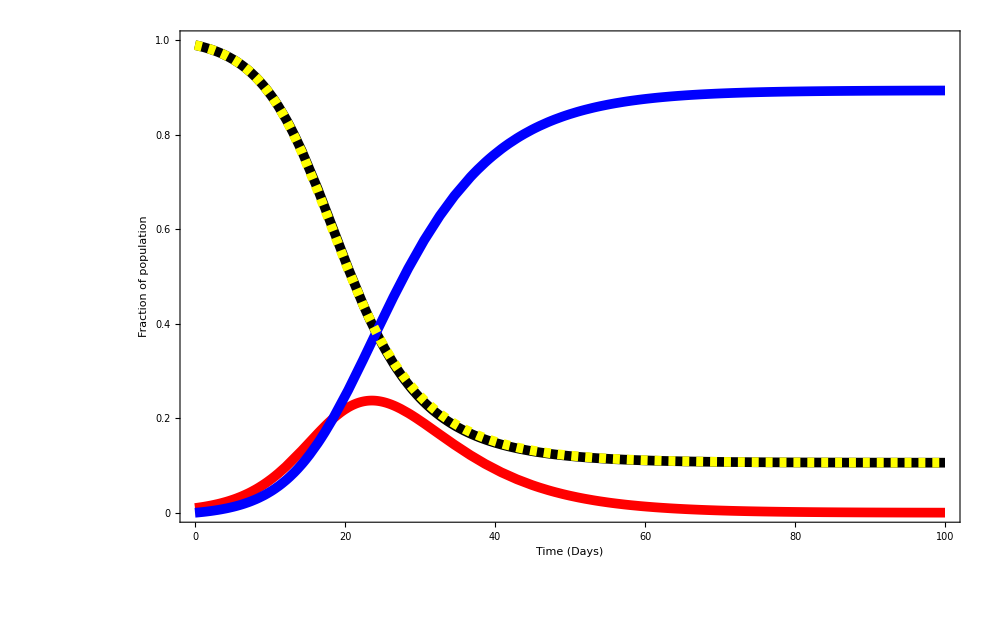

```mathematica
Show[PS0,PI0,PR0,P15]
```

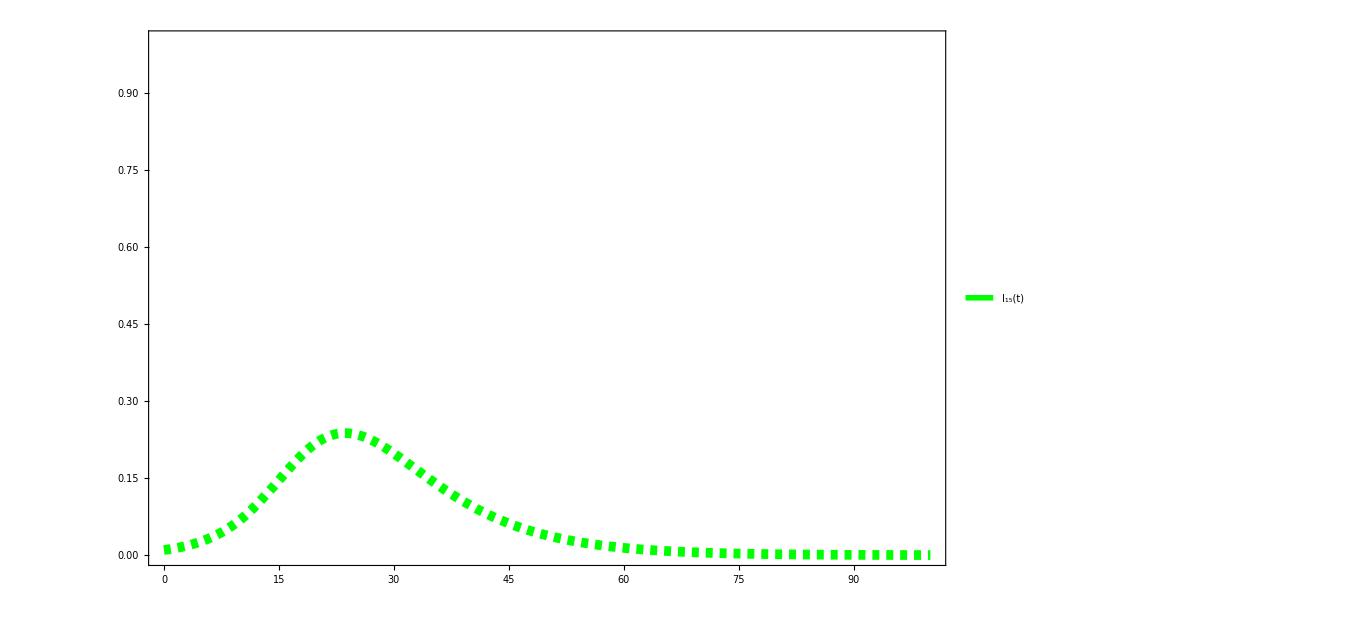

```mathematica
SS15[x_]:=S0*Exp[S15[x]]
II15[t_]:=-SS15[t]+1+(G/B)*Log[SS15[t]/S0]
PI15=Plot[II15[x],{x,0,100},PlotRange->{0,1},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["I_15(t)",Bold,Italic,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

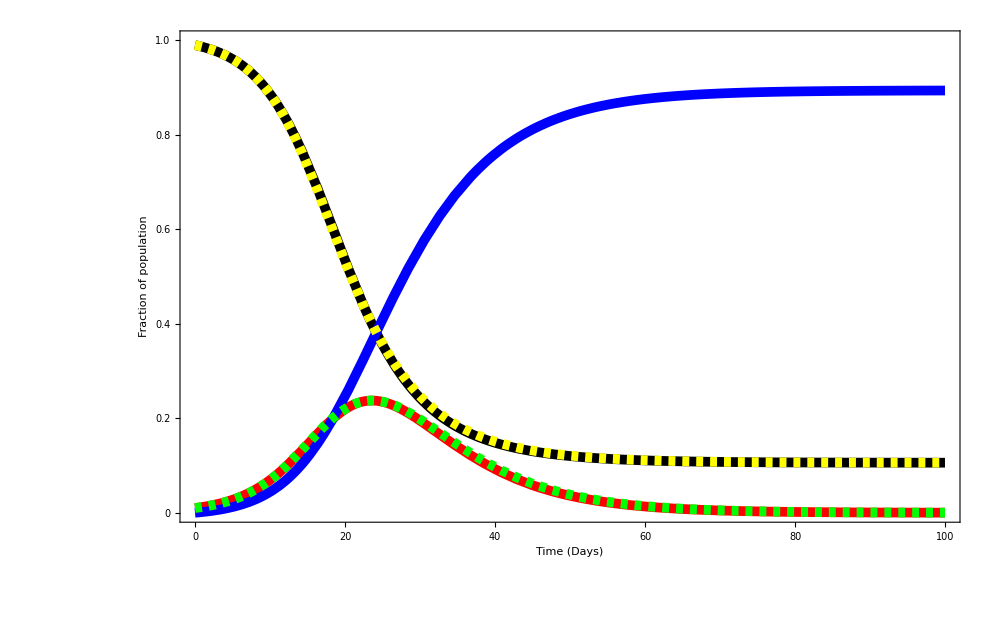

```mathematica
Show[PS0,PI0,PR0,P15,PI15]
```

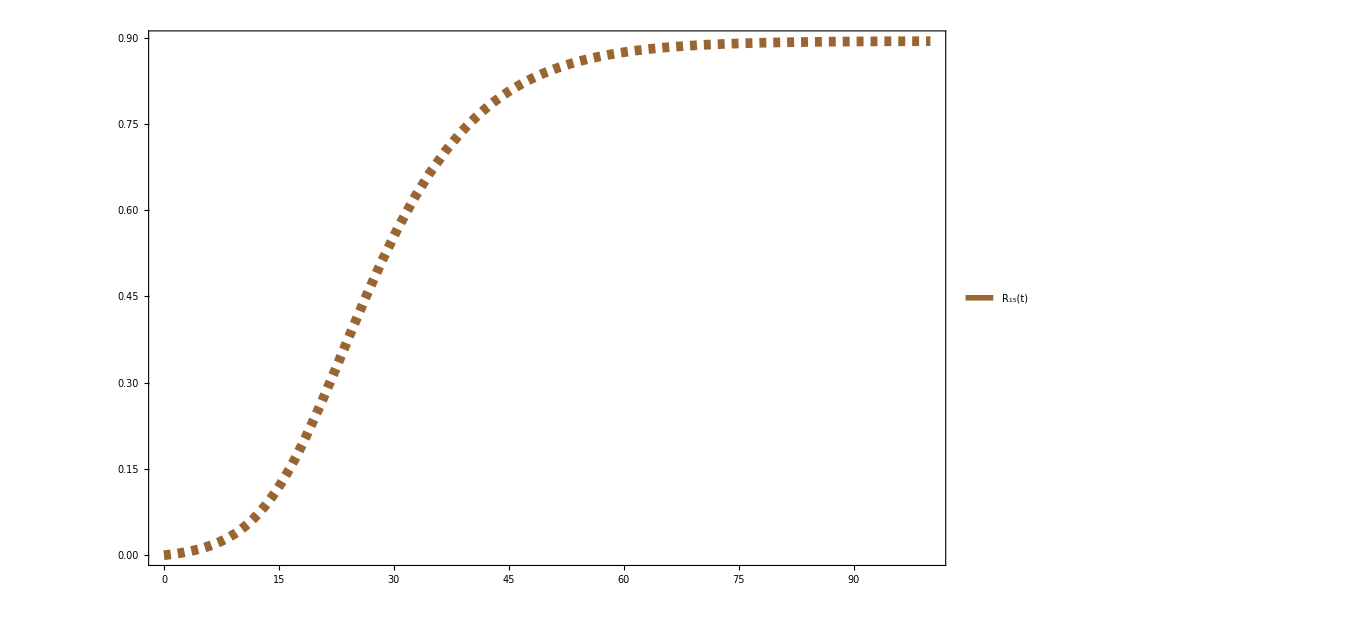

```mathematica
RR15[t_]:=(G/B)*Log[S0/SS15[t]]
PR15=Plot[RR15[x],{x,0,100},
PlotStyle->{Brown,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Brown,Dashed,AbsoluteThickness[5]]},{Style["R_15(t)",Bold,Italic,Black,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

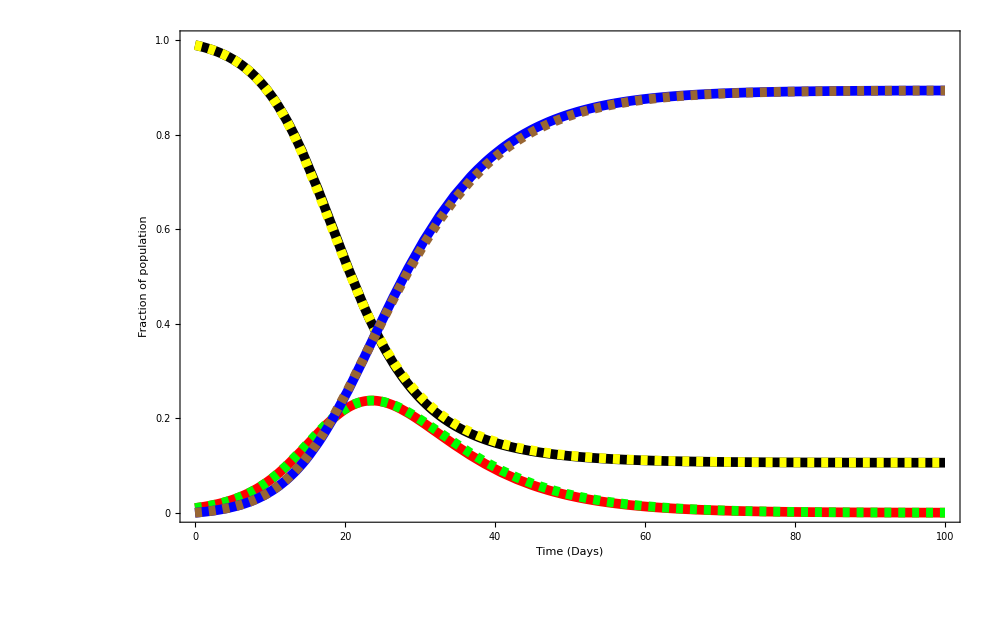

```mathematica
Show[PS0,P15,PI0,PI15,PR0,PR15]
```